```mathematica
SetDirectory[NotebookDirectory[]];
```

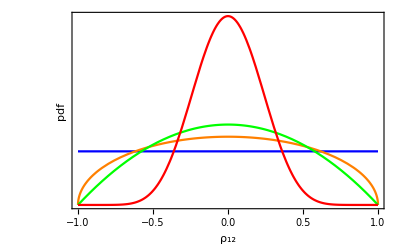

```mathematica
g1=Plot[{PDF[TransformedDistribution[2 u -1,u\[Distributed]BetaDistribution[1,1]],x],PDF[TransformedDistribution[2 u -1,u\[Distributed]BetaDistribution[3/2,3/2]],x],PDF[TransformedDistribution[2 u -1,u\[Distributed]BetaDistribution[2,2]],x],PDF[TransformedDistribution[2 u -1,u\[Distributed]BetaDistribution[10,10]],x]},{x,-1,1},AxesOrigin->{-1,0},PlotStyle->{Blue,Orange,Green,Red},Frame->{True,True,False,False},FrameTicks->{True,False},BaseStyle->Medium,FrameLabel->{"ρ_12","pdf"}]
```

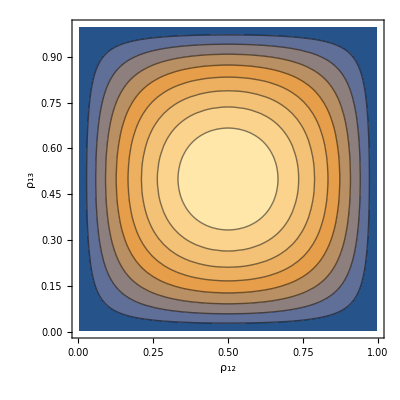

```mathematica
g2=ContourPlot[PDF[BetaDistribution[2,2],x]*PDF[BetaDistribution[2,2],y],{x,0,1},{y,0,1},Frame->{True,True,False,False},FrameLabel->{"ρ_12","ρ_13"},BaseStyle->Medium]
```

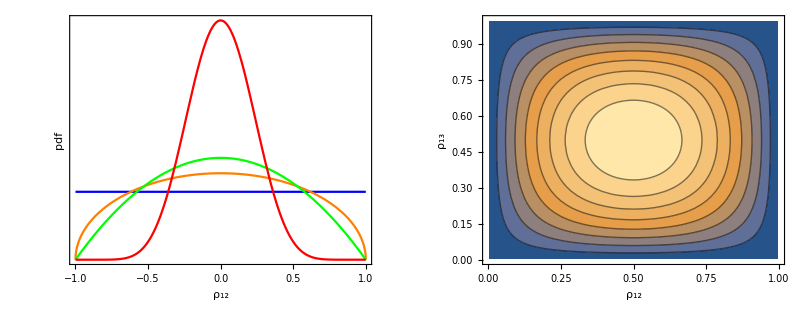

```mathematica
gFinal=Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Export["Distributions_LKJ_correlations.pdf",gFinal]
```

Distributions_LKJ_correlations.pdf